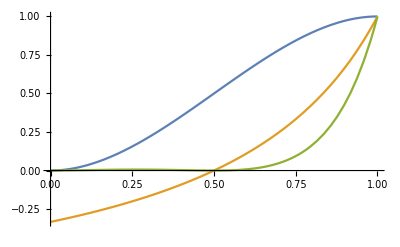

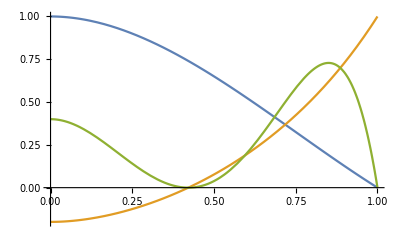

```mathematica
Nmrf[y_]:=.5*2*y^2*(3-2*y)
Amrf[y_]:=(2*y-1)/(3-2*y)
Plot[{Nmrf[x],Amrf[x],Nmrf[x]*Amrf[x]^2},{x,0,1}]

Nlab[y_]:=.2*(y-1)(4*y^2-5*y-5)
Alab[y_]:=(-8*y^2+y+1)/(4*y^2-5*y-5)
Plot[{Nlab[x],Alab[x],10*Nlab[x]*Alab[x]^2},{x,0,1}]
```